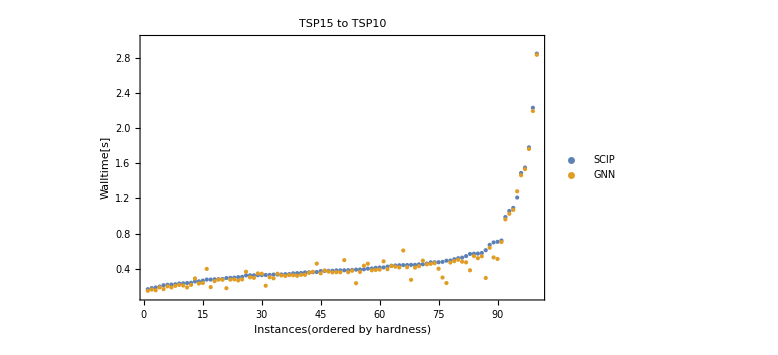

5.79915

```mathematica
data=Import["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/Travel-the-Same-Path/results/15-on-10n_0423-0748.csv", Numeric->True];
data=Delete[data, 1];
{baseline, gnn}=GatherBy[data,First];
baseline=Drop[#,{2,3}]&/@(Drop[#,{1,6}]&/@baseline);
gnn=Drop[#,{2,3}]&/@(Drop[#,{1,6}]&/@gnn);
(*{stime|walltime|proctime}*)
baselineWall=Part[#,2]&/@baseline;
gnnWall=Part[#,2]&/@gnn;
{baselineWall,gnnWall}=SortBy[{baselineWall,gnnWall}ᵀ,First]ᵀ;
plot=Show[
ListPlot[{baselineWall,gnnWall},
Frame->True, FrameLabel->{"Instances(ordered by hardness)","Walltime[s]"},
PlotStyle->PointSize[Medium], 
PlotLegends->Placed[LineLegend[{"SCIP","GNN"}],{0.1,0.9}]],
PlotRange->{Automatic,{0.1,3}},
PlotLabel->Style["TSP15 to TSP10"],
AxesOrigin->{0,0},
ImageSize->Large
]
Export["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/Travel-the-Same-Path/results/Plots/15-10/normal.png",plot];
Mean[baselineWall-gnnWall]/Mean[baselineWall]*100
```

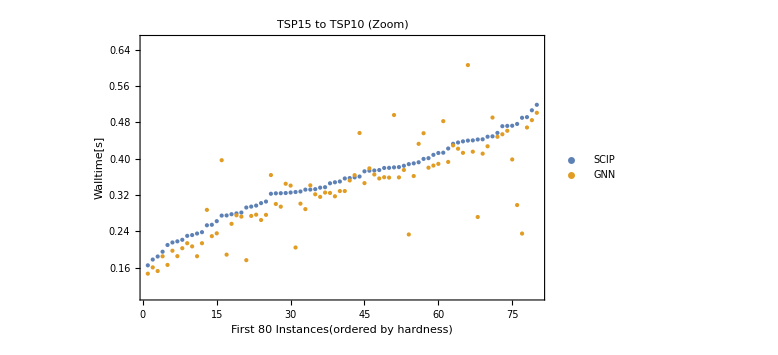

5.59818

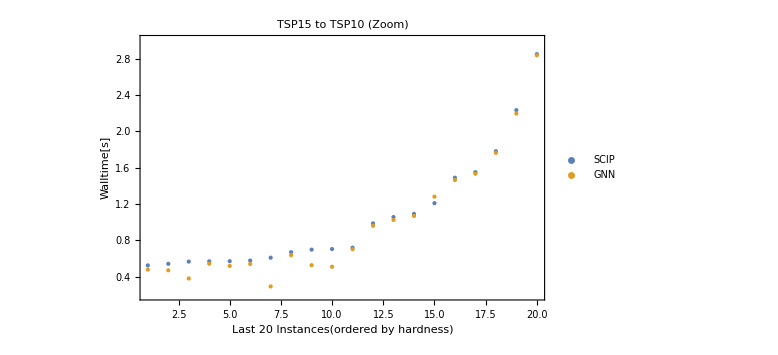

6.06642

```mathematica
plot1=Show[
ListPlot[{baselineWall[[1;;80]],gnnWall[[1;;80]]},
Frame->True, FrameLabel->{"First 80 Instances(ordered by hardness)","Walltime[s]"},
PlotStyle->PointSize[Medium], 
PlotLegends->Placed[LineLegend[{"SCIP","GNN"}],{0.1,0.9}]],
PlotRange->{Automatic,{0.1,0.66}},
PlotLabel->Style["TSP15 to TSP10 (Zoom)"],
AxesOrigin->{0,0},
ImageSize->Large
]
Export["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/Travel-the-Same-Path/results/Plots/15-10/zoom-first80.png",plot1];
Mean[baselineWall[[1;;80]]-gnnWall[[1;;80]]]/Mean[baselineWall[[1;;80]]]*100
plot2=Show[
ListPlot[{baselineWall[[81;;100]],gnnWall[[81;;100]]},
Frame->True, FrameLabel->{"Last 20 Instances(ordered by hardness)","Walltime[s]"},
PlotStyle->PointSize[Medium], 
PlotLegends->Placed[LineLegend[{"SCIP","GNN"}],{0.1,0.9}]],
PlotRange->{Automatic,{0.2,3}},
PlotLabel->Style["TSP15 to TSP10 (Zoom)"],
AxesOrigin->{0,0},
ImageSize->Large
]
Export["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/Travel-the-Same-Path/results/Plots/15-10/zoom-last20.png",plot2];
Mean[baselineWall[[81;;100]]-gnnWall[[81;;100]]]/Mean[baselineWall[[81;;100]]]*100
```